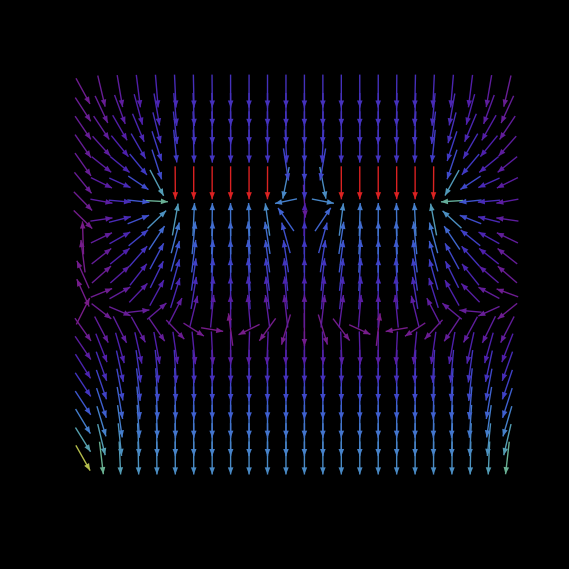

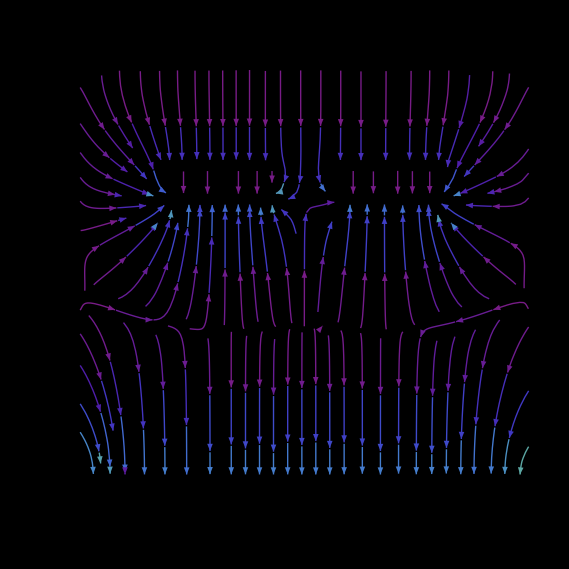

```mathematica
ClearAll["Global`*"]

data = Import["electricField.dat","Table"];
coords = data[[All,{1,2}]];
comps = data[[All,{3,4}]];
Efieldx = data[[All,{3}]];
Efieldy = data[[All,{4}]];

newData = Thread[{coords,comps}];

total = Dimensions[newData][[1]];

plottingData = Take[newData,{1,total,25}];


eField = ListVectorPlot[plottingData,
VectorScale->{Automatic,Automatic,None},
VectorPoints->25,
VectorColorFunctionScaling->True,
VectorColorFunction->"Rainbow",
PlotLegends->BarLegend[{"Rainbow"}], 
Background->Black, 
PerformanceGoal->"Quality",
AspectRatio->1
]

eField = ListStreamPlot[plottingData,
StreamScale->{Automatic,Automatic,None},
StreamColorFunctionScaling->True,
StreamColorFunction->"Rainbow",
PlotLegends->BarLegend[{"Rainbow"}], 
Background->Black, 
PerformanceGoal->"Quality",
AspectRatio->1
]
```